x0=1

Nmax=5

Epsilon =0.0001

f[x] :=Cos[x]

f[x]:=-Sin[x]

In1th Number of iterations the approximation to root is:1.64209

Estimated error is :0.642093

In2th Number of iterations the approximation to root is:1.57068

Estimated error is :0.0714173

In3th Number of iterations the approximation to root is:1.5708

Estimated error is :0.00012105

Return[1.5708]

the final approximation of root is:1.5708

Estimated error is :5.91305×10^-13

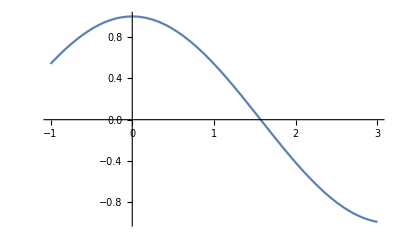

```mathematica
ClearAll;
x0=Input["Enter initial guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter: "];
Print["x0=",x0];
Print["Nmax=",Nmax];
Print["Epsilon =",eps];
f[x_]:=Cos[x];
Print["f[x] :=",f[x]];
Print["f[x]:=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"th Number of iterations the approximation to root is:",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["the final approximation of root is:",x1];
Print["Estimated error is :",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```